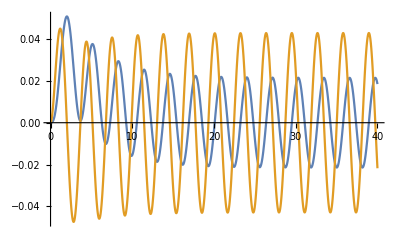

```mathematica
δ = 0.7;
ω =0.5149;
tmax=40;
A =0.1;
sol=NDSolve[{x''[t]+2δ x'[t]+ω^2  x[t]==A Sin[2t],x[0]==0,x'[0]==0},{x[t],x'[t]},{t,0,tmax}];
Plot[Evaluate[{x[t],x'[t]}/.sol],{t,0,tmax}]
```